```mathematica
d = 1.;
Cth = 1.;
a = 1.;

nTerms = 1500;
sepMultMin = 0.5;
sepMultMax = 10000;
sepMultMinHeavi = 1/2000;
sepMultMaxHeavi = 10000000;
nSep = 100;
nSepHeavi = 200;
sepMults =sepMultMin Table[(sepMultMax/sepMultMin)^((i-1)/(nSep-1)),{i,1,nSep}];
sepMultsHeavi =sepMultMinHeavi Table[(sepMultMaxHeavi/sepMultMinHeavi)^((i-1)/(nSepHeavi-1)),{i,1,nSepHeavi}];
seps =sepMults d Cth/a;
sepsHeavi =sepMultsHeavi d Cth/a;

vMFs = 2 Sqrt[(d a)/(seps Cth)];
vMFsHeavi = Sqrt[(d a)/(sepsHeavi Cth)];
gammaScales = Sqrt[a/(d seps Cth)];
```

```mathematica
nGamma = 50;
gMin = 1. gammaScales;
gMax = gammaScales (7.Sqrt[sepMults/200]+1);
vGuess = vMFs (3.5Sqrt[sepMults/200]+1);
gammaVals =Table[Subdivide[gMin[[i]], gMax[[i]], nGamma-1],{i,1,Length[sepMults]}];

waveSpeeds = Table[Table[FindRoot[2 Cth Sqrt[d gammaVals[[j,i]] vee]==1+1/(Exp[seps[[j]] gammaVals[[j,i]]+seps[[j]] Sqrt[gammaVals[[j,i]]vee/d]]-1)+1/(Exp[-seps[[j]] gammaVals[[j,i]]+seps[[j]] Sqrt[gammaVals[[j,i]]vee/d]]-1),{vee,vGuess[[j]]}][[1,2]],{i,1,nGamma}],{j,1,Length[seps]}];

minSpeeds = Table[Min[waveSpeeds[[i]]],{i,1,Length[seps]}];
minSpeedMults = minSpeeds/vMFs;

minSpeedLocs = Flatten[Table[Position[waveSpeeds[[i]],minSpeeds[[i]]],{i,1,Length[waveSpeeds]}]];
minGammas = Table[gammaVals[[i,minSpeedLocs[[i]]]],{i,1,Length[minSpeedLocs]}];

waveSpeedsHeavi = Table[FindRoot[Cth==sepsHeavi[[j]]/(2d)Sum[((4 i d)/(Pi vee sepsHeavi[[j]]))^(1/2)Exp[-(i vee sepsHeavi[[j]])/(4 d)]-i Erfc[((i vee sepsHeavi[[j]])/(4 d))^(1/2)],{i,1,nTerms}],{vee,0.05vMFsHeavi[[j]]}][[1,2]],{j,1,Length[sepsHeavi]}];
waveSpeedMultsHeavi = waveSpeedsHeavi/vMFsHeavi;
```

General::munfl: 1/(5.32195×10^307) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/(1.18681×10^308) is too small to represent as a normalized machine number; precision may be lost.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::munfl: Exp[-720.667] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-720.186] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-719.706] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
timeFunc = Interpolation[Transpose[{seps,seps/minSpeeds}],InterpolationOrder->1];
timeFuncHeavi = Interpolation[Transpose[{sepsHeavi,sepsHeavi/waveSpeedsHeavi}],InterpolationOrder->1];
pDist[x_,d_]:=Exp[-x/d]/d;

waveSpeedsDisordered = seps/Table[NIntegrate[timeFunc[x]pDist[x,seps[[i]]],{x,Min[seps],Max[seps]}],{i,1,Length[seps]}];
waveSpeedsDisorderedHeavi = sepsHeavi/Table[NIntegrate[timeFuncHeavi[x]pDist[x,sepsHeavi[[i]]],{x,Min[sepsHeavi],Max[sepsHeavi]}],{i,1,Length[sepsHeavi]}];
```

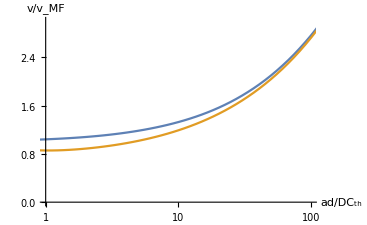

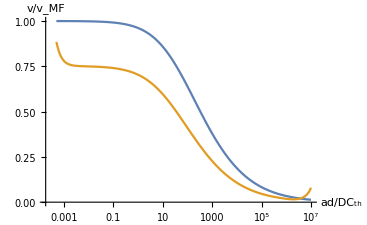

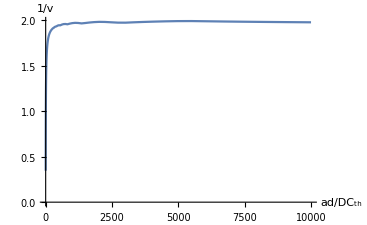

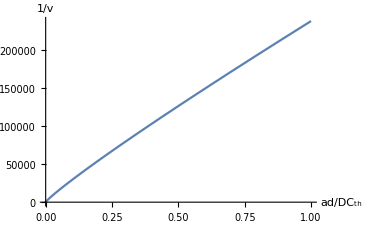

```mathematica
ListLogLinearPlot[{Transpose[{sepMults,minSpeedMults}],Transpose[{sepMults,waveSpeedsDisordered/vMFs}]},Joined->True,AxesLabel->{"ad/DC_th","v/v_MF"},PlotRange->{{1,100},{0,3}}]
ListLogLinearPlot[{Transpose[{sepMultsHeavi,waveSpeedMultsHeavi}],Transpose[{sepMultsHeavi,waveSpeedsDisorderedHeavi/vMFsHeavi}]},Joined->True,AxesLabel->{"ad/DC_th","v/v_MF"},PlotRange->All]

ListPlot[Transpose[{sepMults,1/minSpeeds}],Joined->True,AxesLabel->{"ad/DC_th","1/v"},PlotRange->All]
ListPlot[Transpose[{sepMultsHeavi,1/waveSpeedsHeavi}],Joined->True,AxesLabel->{"ad/DC_th","1/v"},PlotRange->All]
```

```mathematica
numericsDisordered1 = {{1.,2.1,4.5,10.,21.,45.,100.},{1.0184102096370553,1.0889765559511122,1.2095557185958663,1.382513773729586,1.6860567873172227,2.053522403565534,2.7893657317550056}};
numericsDisorderedInf = {{0.01,0.1,1.,10.,100.,1000.,10000.,100000.,1000000.},{0.9708649081754902,0.9328126390022144,0.8780489236338908,0.6923180123275964,0.44327726281101476,0.23277638443097515,0.10831437148017707,0.04371807034944297,0.018219297259383187}};
```

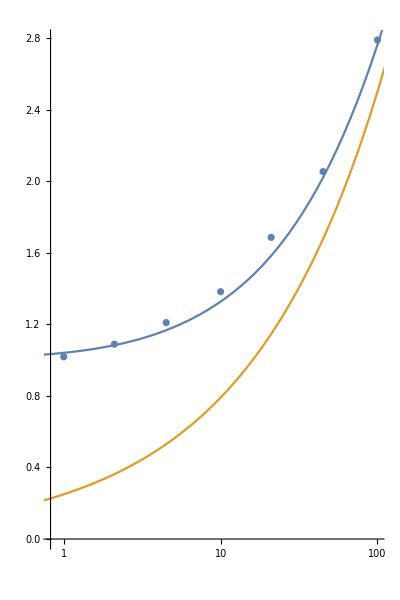

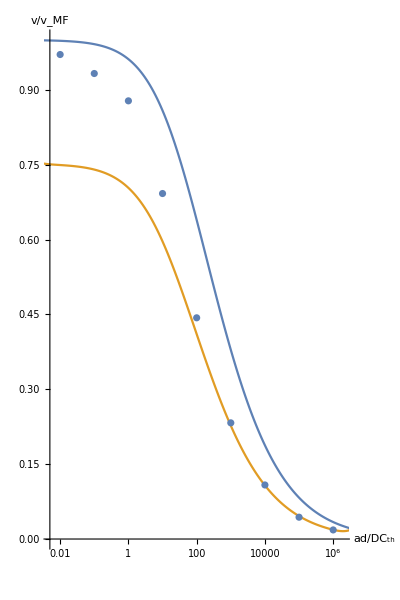

```mathematica
Show[ListLogLinearPlot[Transpose[numericsDisordered1]],ListLogLinearPlot[{Transpose[{sepMults,minSpeedMults}],Transpose[{sepMults,(a/2/Cth)/vMFs}]},Joined->True,AxesLabel->{"ad/DC_th","v/v_MF"},PlotRange->{{1,100},{0,3}}],AspectRatio->1.5]
Show[ListLogLinearPlot[{Transpose[{sepMultsHeavi,waveSpeedMultsHeavi}],Transpose[{sepMultsHeavi,waveSpeedsDisorderedHeavi/vMFsHeavi}]},Joined->True,AxesLabel->{"ad/DC_th","v/v_MF"},PlotRange->{{1/200,2000000},{0,1}}],ListLogLinearPlot[Transpose[numericsDisorderedInf]],AspectRatio->1.5]
```

```mathematica
plotColors = {RGBColor[0.5, 0.5, 1.],RGBColor[0., 0., 0.]};
dashedColor = RGBColor[0.6,0.6,0.6];

wid = 1750;
hei = 2500;
aR = hei/wid;
minorThickness = Thickness[20/wid];
majorThickness = Thickness[25/wid];
majorMajorThickness = Thickness[30/wid];
tL = 75/wid;
fS = Directive[Black,minorThickness];
tS = Directive[Black,minorThickness];
markerSize = wid/18;
markerPrefs = Table[Graphics[{plotColors[[i]],Thickness[0.15],Circle[]}, ImageSize->markerSize],{i,1,2}];

pR = {{1/2,200},{0,3}};
pRClip = {10,200};
pR2 ={{1/200,2000000},{0,1}};
pRClip2 = {30,2000000};
fT = {{{#,"",{tL,0}}&/@{1,2},None},{{#,"",{tL,0}}&/@{1,10,100},None}};
fT2 = {{{#,"",{tL,0}}&/@{0.5},None},{{#,"",{tL,0}}&/@{0.1,100,100000},None}};

plotFunc1 = Interpolation[Transpose[{sepMults,(a/2/Cth)/vMFs}],InterpolationOrder->1];
plotFuncInf = Interpolation[Transpose[{sepMultsHeavi,waveSpeedsDisorderedHeavi/vMFsHeavi}],InterpolationOrder->1];
```

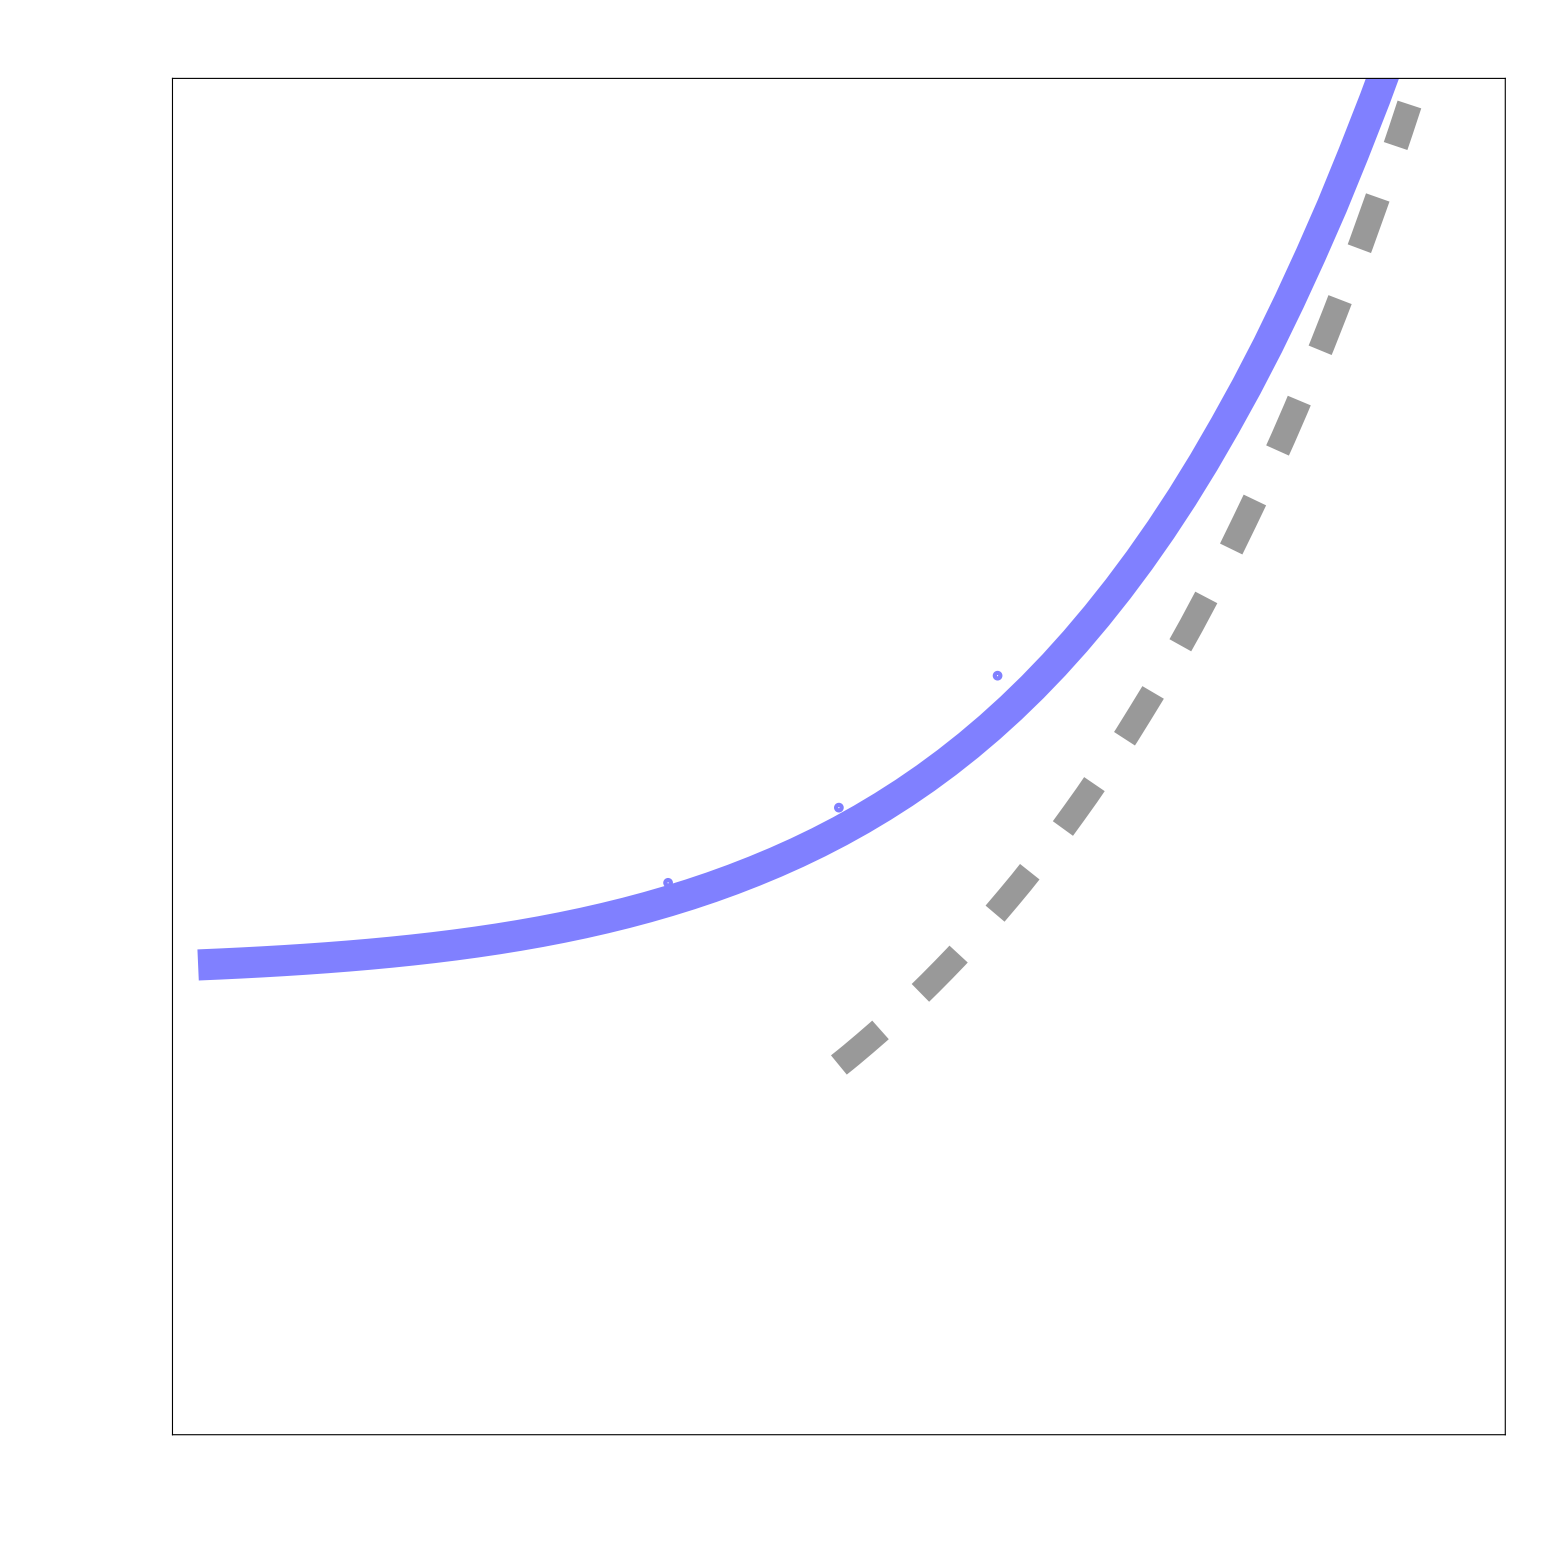

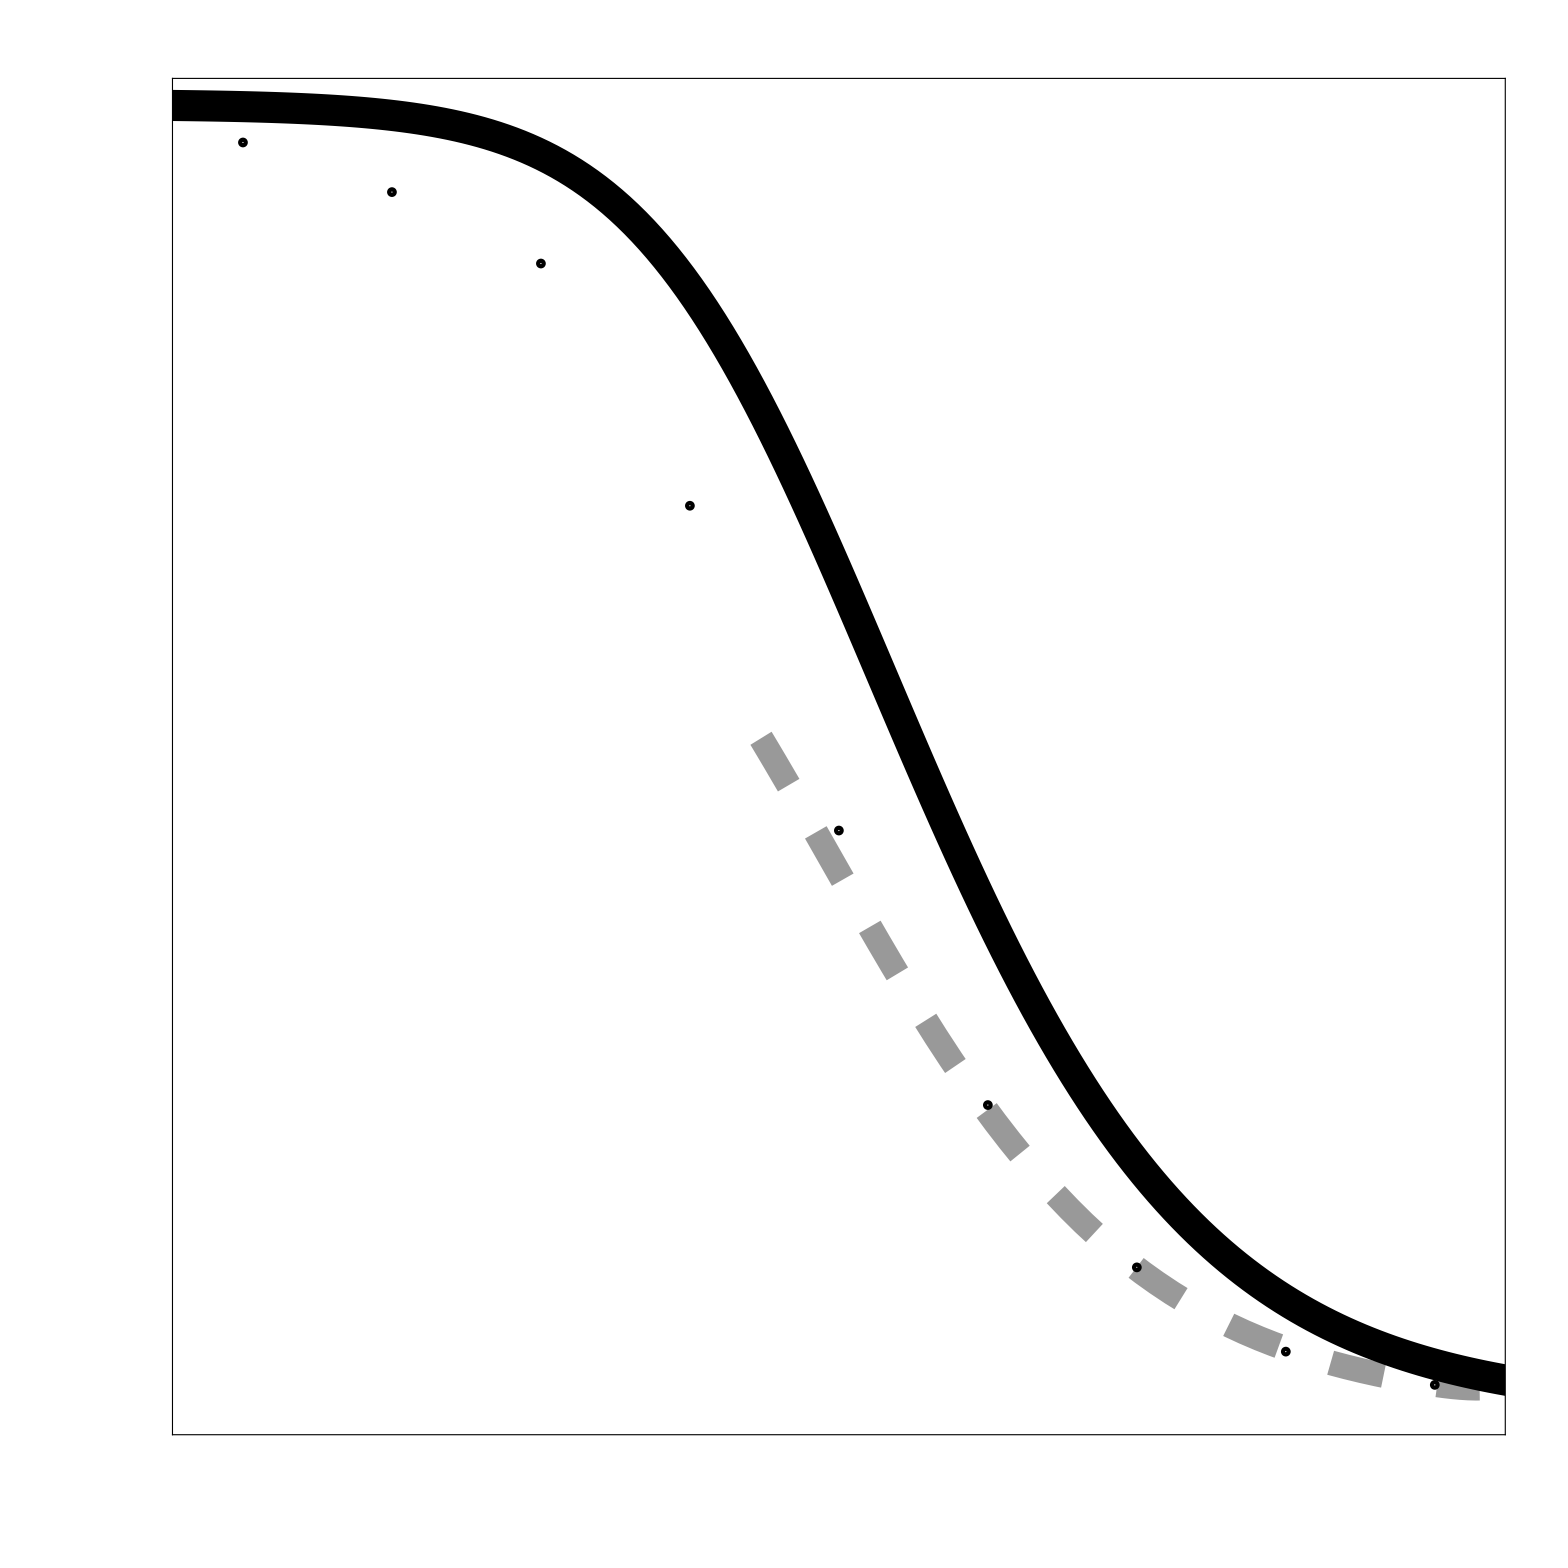

```mathematica
waveSpeedPlotn1Disordered = Show[LogLinearPlot[plotFunc1[x],{x,pRClip[[1]],pRClip[[2]]},PlotRange->pR,Frame->True,FrameStyle->fS,FrameTicks->fT,PlotStyle->{dashedColor,Dashing[{0.025,0.025}],minorThickness}],ListLogLinearPlot[Transpose[{sepMults,minSpeedMults}],Joined->True,PlotStyle->{plotColors[[1]],majorThickness}],ListLogLinearPlot[Transpose[numericsDisordered1],PlotMarkers->markerPrefs[[1]]],AspectRatio->aR,ImageSize->wid]

waveSpeedPlotnInfDisordered = Show[LogLinearPlot[plotFuncInf[x],{x,pRClip2[[1]],pRClip2[[2]]},PlotRange->pR2,Frame->True,FrameStyle->fS,FrameTicks->fT2,PlotStyle->{dashedColor,Dashing[{0.025,0.025}],minorThickness}],ListLogLinearPlot[Transpose[{sepMultsHeavi,waveSpeedMultsHeavi}],Joined->True,PlotStyle->{plotColors[[2]],majorThickness}],ListLogLinearPlot[Transpose[numericsDisorderedInf],PlotMarkers->markerPrefs[[2]]],AspectRatio->aR,ImageSize->wid]
```

```mathematica
Export["waveSpeedPlotn1Disordered.pdf",waveSpeedPlotn1Disordered]
```

waveSpeedPlotn1Disordered.pdf

```mathematica
Export["waveSpeedPlotnInfDisordered.pdf",waveSpeedPlotnInfDisordered]
```

waveSpeedPlotnInfDisordered.pdf